```mathematica
Quit
```

## Find the paclet

```mathematica
If[$VersionNumber≥12.1,
PacletDirectoryLoad@FileNameJoin[{FileNameDrop@NotebookDirectory[],"COVID19"}],
PacletManager`PacletDirectoryAdd@FileNameJoin[{FileNameDrop@NotebookDirectory[],"COVID19"}]
];
```

## Growth Plots for US Counties

#### Choose some counties using anything that passes Interpreter[“USCounty”]

The first evaluation is very slow for importing and interpreting data, but subsequent evaluations are much faster

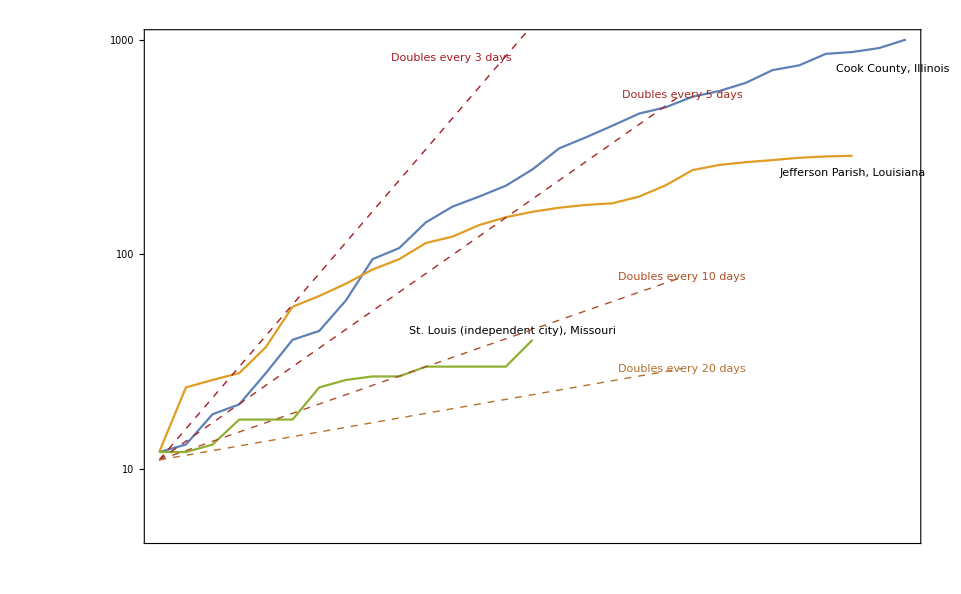

```mathematica
COVID19`USCountyGrowthPlot[{"Cook County, IL","Jefferson Parish, LA","St. Louis City"}]
```

#### Automatically choose the most affected counties

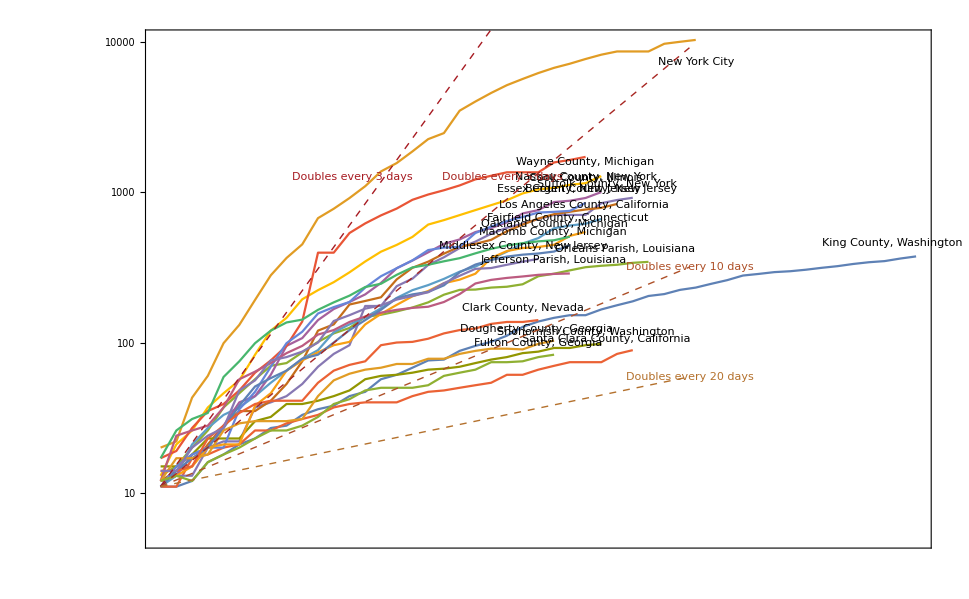

```mathematica
COVID19`USCountyGrowthPlot[]
```

## US Metro Area Plots and Data Table

#### I (Bob S) live in St. Louis, so I got this working. It should be easy to do the same for others

```mathematica
{plots, table}=COVID19`MetroData["STL","MetroName"->"St. Louis "];
```

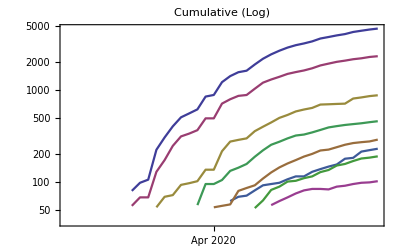
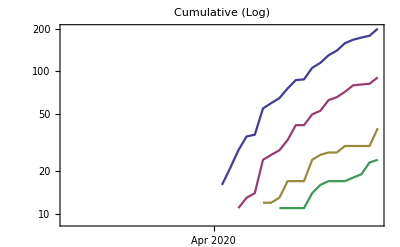
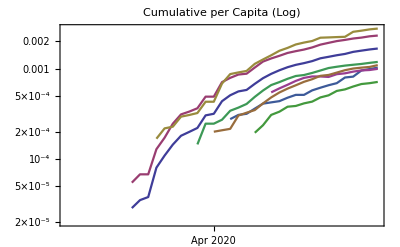
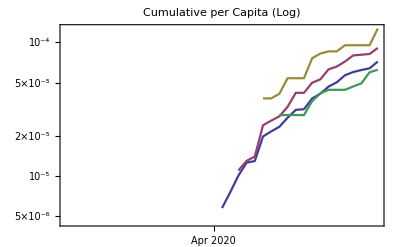
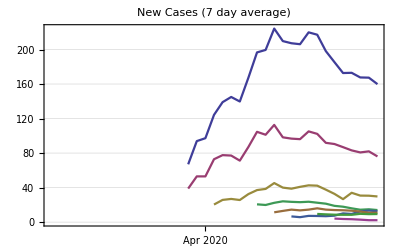
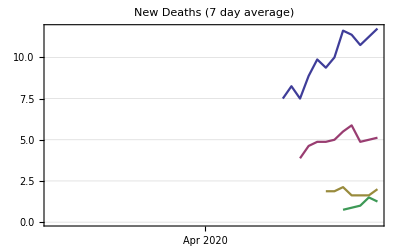
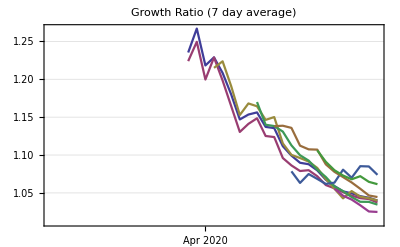
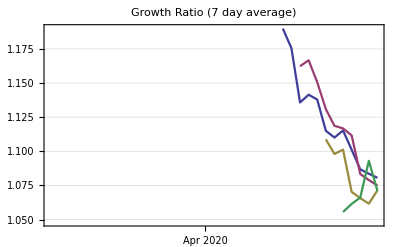
St. Louis Metro Area COVID-19 Timelines
From NY Times data on Tue 21 Apr 2020 |  | 
Cases (> 50) | Deaths (> 10) | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
plots
```

```mathematica
table
```

Tuesday 21 April 2020

#### Create a public web page with this info:

```mathematica
COVID19`DeployMetroData["STL","COVID19/STLMetro/TimelineGridAndDataTable","MetroName"->"St. Louis "]
```

CloudObject[https://www.wolframcloud.com/obj/wolframphysics/COVID19/STLMetro/TimelineGridAndDataTable]

## Testing data

#### This source seems to have quality data, but I haven’t made TimeSeries yet.

```mathematica
testingdata=COVID19`OurWorldInDataTestingData["New"]
```

## Create Plots and Data Tables for Countries

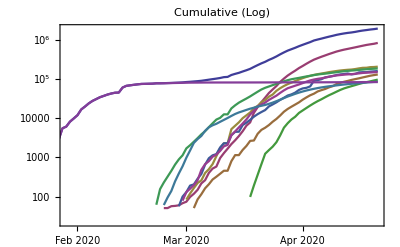
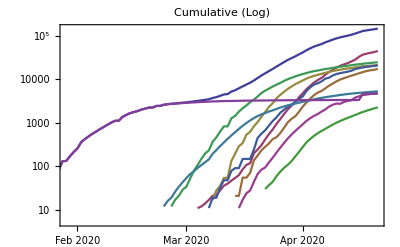
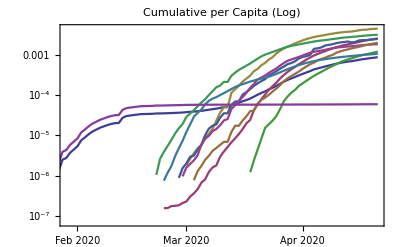
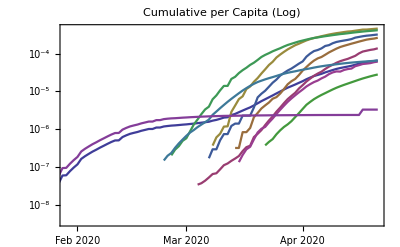
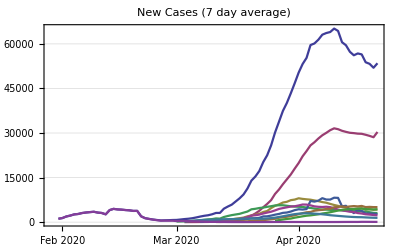
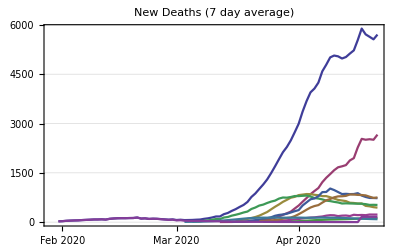
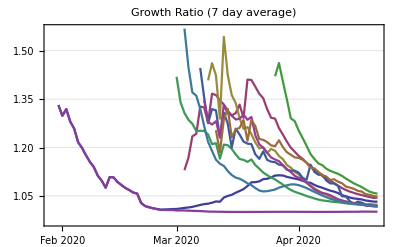
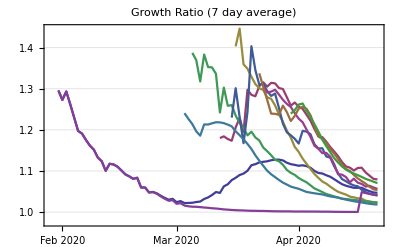
{COVID-19 Timelines
From NY Times data on Tue 21 Apr 2020 |  | 
Cases (> 50) | Deaths (> 10) | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | ,Tuesday 21 April 2020}

```mathematica
COVID19`CountryPlotsAndData[Automatic]
```